```mathematica
Sum[((-1)^(n+1) x^(2n))/((2 n)!),{n,0,Infinity}]
```

-Cos[x]

```mathematica
Series[-Cos[x],{x,0,4}]
```

-1+x^2/2-x^4/24+O[x]^5

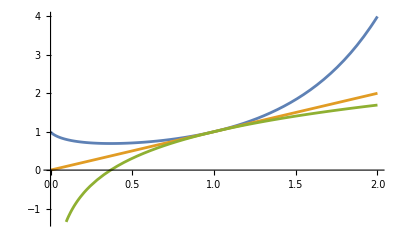

```mathematica
Plot[{x^x,x, Log[x]+1},{x,0,2}]
```

```mathematica
D[D[x^x - Log[x]-1,x],x]
```

1/x^2+x^(-1+x)+x^x (1+Log[x])^2

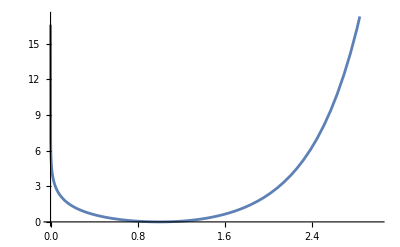

```mathematica
Plot[x^x - Log[x]-1,{x,0,3}]
```

```mathematica
Subscript[ω, q] == (Sqrt[8 Subscript[e, c] Subscript[e, J]] - Subscript[e, c])/ℏ
Subscript[e, J]==(Subscript[Φ, 0]/(2 π))^2 1/Subscript[L, J]
```

```mathematica
Subscript[ω, q] == (Sqrt[8 Subscript[e, c] Subscript[e, J]] - Subscript[e, c])/ℏ/.{Subscript[e, J]->(Subscript[Φ, 0]/(2 π))^2 1/Subscript[L, J]}
```

ω_q==(-e_c+(√2 √((e_c Φ_0^2)/L_J))/π)/ℏ

```mathematica
Solve[Subscript[ω, q]==(-Subscript[e, c]+(√2 √((Subscript[e, c] Subscript[Φ, 0]^2)/Subscript[L, J]))/π)/ℏ,Subscript[L, J]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{L_J→(2 e_c Φ_0^2)/(π^2 (e_c+ℏ ω_q)^2)}}

```mathematica
Simplify[D[(-Subscript[e, c]+(√2 √((Subscript[e, c] Subscript[Φ, 0]^2)/Subscript[L, J]))/π)/ℏ,Subscript[L, J]],{Subscript[L, J]>0,Subscript[Φ, 0]>0}]
```

-(√e_c Φ_0)/(√2 π ℏ L_J^(3/2))

```mathematica
D[(2 Subscript[e, c] Subscript[Φ, 0]^2)/(π^2 (Subscript[e, c]+ℏ Subscript[ω, q])^2),Subscript[ω, q]]//Simplify
```

-(4 ℏ e_c Φ_0^2)/(π^2 (e_c+ℏ ω_q)^3)

```mathematica
Γ = {{Subscript[γ, 1], Sqrt[Subscript[γ, 1] Subscript[γ, 2]]/2 (Sqrt[Subscript[ω, 1]/Subscript[ω, 2]] Exp[ⅈ Subscript[ω, 1] Subscript[t, 12]]+Sqrt[Subscript[ω, 2]/Subscript[ω, 1]] Exp[-ⅈ Subscript[ω, 2] Subscript[t, 12]])},
{Sqrt[Subscript[γ, 1] Subscript[γ, 2]]/2 (Sqrt[Subscript[ω, 1]/Subscript[ω, 2]] Exp[-ⅈ Subscript[ω, 1] Subscript[t, 12]]+Sqrt[Subscript[ω, 2]/Subscript[ω, 1]] Exp[ⅈ Subscript[ω, 2] Subscript[t, 12]]),Subscript[γ, 2]}}
```

{{γ_1,1/2 √(γ_1 γ_2) (ⅇ^(ⅈ t_12 ω_1) √(ω_1/ω_2)+ⅇ^(-ⅈ t_12 ω_2) √(ω_2/ω_1))},{1/2 √(γ_1 γ_2) (ⅇ^(-ⅈ t_12 ω_1) √(ω_1/ω_2)+ⅇ^(ⅈ t_12 ω_2) √(ω_2/ω_1)),γ_2}}

```mathematica
Γs = FullSimplify[Γ/.{Subscript[ω, 1]->Subscript[ω, d],Subscript[ω, 2]->Subscript[ω, d]}]
```

{{γ_1,Cos[t_12 ω_d] √(γ_1 γ_2)},{Cos[t_12 ω_d] √(γ_1 γ_2),γ_2}}

```mathematica
{gD,gB} = FullSimplify[Eigenvalues[Γs]/.{Subscript[t, 12]->(π-δ)/Subscript[γ, 1]},{Subscript[γ, 1]>0, Subscript[γ, 2]>0, Subscript[ω, 1]>0, Subscript[ω, 2]>0,Subscript[t, 12]>0}]
```

{1/2 (γ_1+γ_2-√(γ_1^2+2 Cos[(2 (π-δ) ω_d)/γ_1] γ_1 γ_2+γ_2^2)),1/2 (γ_1+γ_2+√(γ_1^2+2 Cos[(2 (π-δ) ω_d)/γ_1] γ_1 γ_2+γ_2^2))}

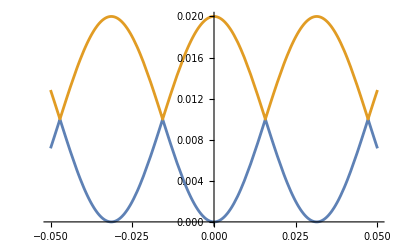

```mathematica
Plot[Evaluate@({gD, gB}/.{Subscript[γ, 1]->0.01, Subscript[γ, 2]->0.01,Subscript[ω, d]->1}),{δ,-0.05,0.05}]
```

```mathematica
(2 (π-δ) Subscript[ω, d])/Subscript[γ, 1]
```

```mathematica
(π Subscript[γ, 1])/Subscript[ω, d]/.{Subscript[γ, 1]->0.01, Subscript[γ, 2]->0.01,Subscript[ω, d]->1}
```

0.0314159

```mathematica
gD
```

1/2 (γ_1+γ_2-√(γ_1^2+2 Cos[(2 (π-δ) ω_d)/γ_1] γ_1 γ_2+γ_2^2))

```mathematica
FullSimplify[gD/.{Subscript[γ, 1]->γ,Subscript[γ, 2]->γ},{Subscript[L, J]>0,cof>0,Subscript[e, c]>0,γ>0}]
```

γ-γ √(Cos[((π-δ) ω_d)/γ]^2)

```mathematica
FullSimplify[(gD/.{δ->(Subscript[ω, 1]-Subscript[ω, d])/Subscript[γ, 1]})/.{Subscript[ω, 1]->(-Subscript[e, c]+cof √((8 Subscript[e, c])/Subscript[L, J]))/ℏ,Subscript[γ, 1]->γ,Subscript[γ, 2]->γ},{Subscript[L, J]>0,cof>0,Subscript[e, c]>0,γ>0}]
```

γ-γ √(Cos[(ω_d (π γ ℏ+e_c-2 √2 cof √(e_c/L_J)+ℏ ω_d))/(γ^2 ℏ)]^2)

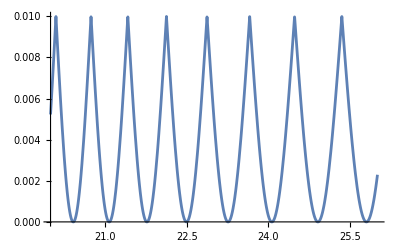

```mathematica
Plot[1/2 (Subscript[γ, 1]+Subscript[γ, 2]-√(Subscript[γ, 1]^2+2 Cos[(2 Subscript[ω, d] (π Subscript[e, c]+π^2 ℏ Subscript[γ, 1]-√2 √(Subscript[e, c]/Subscript[L, J]) Subscript[Φ, 0]+π ℏ Subscript[ω, d]))/(π ℏ Subscript[γ, 1]^2)] Subscript[γ, 1] Subscript[γ, 2]+Subscript[γ, 2]^2))/.{Subscript[γ, 1]->0.01,Subscript[γ, 2]->0.01, Subscript[ω, d]->1,Subscript[e, c]->0.04,ℏ->1,Subscript[Φ, 0]->1},{Subscript[L, J],20,26}]
```

```mathematica
Series[1/(L0+dL),{dL,0,1}]
```

1/L0-dL/L0^2+O[dL]^2

```mathematica
Series[(Subscript[ω, d] (-2 √2 cof √(Subscript[e, c]/(Subscript[L, J0]+dL))))/(γ^2 ℏ),{dL,0,1}]
```

-(2 (√2 cof √(e_c/L_J0) ω_d))/(γ^2 ℏ)+(√2 cof √(e_c/L_J0) ω_d dL)/(γ^2 ℏ L_J0)+O[dL]^2

```mathematica
FullSimplify[(2π)/((√2 cof √(Subscript[e, c]/Subscript[L, J0]) Subscript[ω, d])/(γ^2 ℏ Subscript[L, J0])),{Subscript[L, J]>0,cof>0,Subscript[e, c]>0,γ>0}]
```

(√2 π γ^2 ℏ L_J0)/(cof √(e_c/L_J0) ω_d)

```mathematica
f[i_]:={HeavisideTheta[(-1)^(i+1)],HeavisideTheta[(-1)^i]}
```

```mathematica
f[2]
```

{0,1}

```mathematica
a[j_]:=(-1)^(j+1)/Sqrt[2] ϵ;
aa[i_,j_]:=β/2 +μ/2 (-1)^(i+j);
```

```mathematica
tran = 1+Sum[Sqrt[Subscript[γ, j]/2]*2*Re[a[j]*Exp[ⅈ Subscript[ω, j] Subscript[t, j]]],{j,1,2}]/ain+1/ain^2 Sum[Sqrt[Subscript[γ, i] Subscript[γ, j]]/2 aa[i,j] Exp[-ⅈ (Subscript[ω, i] Subscript[t, i] - Subscript[ω, j] Subscript[t, j])],{i,1,2},{j,1,2}]
```

1+(Re[ⅇ^(ⅈ t_1 ω_1) ϵ] √γ_1-Re[ⅇ^(ⅈ t_2 ω_2) ϵ] √γ_2)/ain+1/ain^2(1/2 (β/2+μ/2) √(γ_1^2)+1/2 ⅇ^(-ⅈ (t_1 ω_1-t_2 ω_2)) (β/2-μ/2) √(γ_1 γ_2)+1/2 ⅇ^(-ⅈ (-t_1 ω_1+t_2 ω_2)) (β/2-μ/2) √(γ_1 γ_2)+1/2 (β/2+μ/2) √(γ_2^2))

```mathematica
FullSimplify[ComplexExpand[Simplify[1+Sum[Sqrt[Subscript[γ, j]/2]*a[j]*Exp[ⅈ Subscript[ω, j] Subscript[t, j]],{j,1,2}]/ain/.{Subscript[γ, 1]->γ,Subscript[γ, 2]->γ}],ϵ],{γ>0}]
```

1+((ⅇ^(ⅈ t_1 ω_1)-ⅇ^(ⅈ t_2 ω_2)) √γ ϵ)/(2 ain)

```mathematica
tranSim = FullSimplify[tran/.{Subscript[γ, 1]->γ,Subscript[γ, 2]->γ(*,Subscript[t, 1]->0,Subscript[t, 2]->(π-δ)/w*)},{β>=0,γ>0,μ>0,w>0,δ∈Reals}]
```

(ain^2+1/2 γ (β+μ)+1/2 γ (β-μ) Cos[t_1 ω_1-t_2 ω_2]+ain √γ Re[(ⅇ^(ⅈ t_1 ω_1)-ⅇ^(ⅈ t_2 ω_2)) ϵ])/ain^2

```mathematica
Series[tranSim/.{ϵ->0,μ->0},{δ,0,2}]
```

(2 ain^2+β γ+β γ Cos[(π ω_2)/w])/(2 ain^2)+(β γ Sin[(π ω_2)/w] ω_2 δ)/(2 ain^2 w)-((β γ Cos[(π ω_2)/w] ω_2^2) δ^2)/(4 (ain^2 w^2))+O[δ]^3

```mathematica
tranSim/.{ain->0.05,γ->0.01,Subscript[ω, 2]->1+0.1*0.001, w->1,δ->-0.1,μ->0,ϵ->-0.05745237-0.00126442 ⅈ,β->2/3}
```

0.777219

```mathematica
tranSim/.{γ->0.01,Subscript[ω, 2]->1+0.1*0.001, w->1,δ->-0.1,μ->0,ϵ->-0.05745237-0.00126442 ⅈ}
```

(-0.0228978 ain+2 ain^2+0.0000502825 β)/(2 ain^2)

```mathematica
S1 = KroneckerProduct[{{0,0},{1,0}},DiagonalMatrix[{1,1}]]
S2 = KroneckerProduct[DiagonalMatrix[{1,1}],{{0,0},{1,0}}]
```

{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}}

{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,0,1,0}}

```mathematica
ρss=({{0, 0, 0, 0}, {0, μ, 0, ϵ}, {0, 0, β, 0}, {0, ϵ*, 0, α}});
Atr=({{1, 0, 0, 0}, {0, 1/(√2), 1/(√2), 0}, {0, -1/(√2), 1/(√2), 0}, {0, 0, 0, 1}});
```

```mathematica
Atr.({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 2/3, 0}, {0, 0, 0, 1/3}}).Atrᵀ
```

{{0,0,0,0},{0,1/3,1/3,0},{0,1/3,1/3,0},{0,0,0,1/3}}

```mathematica
Tr[S1ᵀ.S2.Atr.ρss.Atrᵀ]
```

β/2-μ/2

```mathematica
aL = ain*DiagonalMatrix[{1,1,1,1}]+Sqrt[γ/2] S1 Exp[ⅈ Subscript[ω, 1] Subscript[t, 1]]+Sqrt[γ/2] S2 Exp[ⅈ Subscript[ω, 2] Subscript[t, 2]]
```

{{ain,0,0,0},{(ⅇ^(ⅈ t_2 ω_2) √γ)/(√2),ain,0,0},{(ⅇ^(ⅈ t_1 ω_1) √γ)/(√2),0,ain,0},{0,(ⅇ^(ⅈ t_1 ω_1) √γ)/(√2),(ⅇ^(ⅈ t_2 ω_2) √γ)/(√2),ain}}

```mathematica
FullSimplify[ComplexExpand[1/ain Tr[aL.{{0,0,0,0},{0,1/3,1/3,0},{0,1/3,1/3,0},{0,0,0,1/3}}],ϵ],{ain>0,γ>0,Subscript[ω, 1]>0,Subscript[t, 1]∈Reals,Subscript[ω, 2]>0,Subscript[t, 2]∈Reals,μ>=0,β>=0,α>=0}]
```

1

```mathematica
tranAl = FullSimplify[ComplexExpand[Tr[ConjugateTranspose[aL].aL.Atr.ρss.Atrᵀ]/ain^2,ϵ],{ain>0,γ>0,Subscript[ω, 1]>0,Subscript[t, 1]∈Reals,Subscript[ω, 2]>0,Subscript[t, 2]∈Reals,μ>=0,β>=0,α>=0}]
```

1/(2 ain^2)(γ (β+μ)+2 ain^2 (α+β+μ)+γ (β-μ) Cos[t_1 ω_1-t_2 ω_2]+2 ain √γ ((Cos[t_1 ω_1]-Cos[t_2 ω_2]) Re[ϵ]+Im[ϵ] (-Sin[t_1 ω_1]+Sin[t_2 ω_2])))

```mathematica
FullSimplify[tranAl/.{Subscript[t, 1]->0,Subscript[t, 2]->(π-δ)/w},{β>=0,γ>0,μ>0,w>0,δ∈Reals}]
```

α+β-((-1+ⅇ^((ⅈ (π-δ) ω_2)/w)) √γ ϵ)/(2 ain)+μ

```mathematica
FullSimplify[tranAl/.{Subscript[t, 1]->0,Subscript[t, 2]->(π-δ)/w},{β>=0,γ>0,μ>0,w>0,δ∈Reals}]/.{γ->10^-2,Subscript[ω, 2]->1, w->1,δ->-10^-1,μ->0,ϵ->0,α->1/2 β}
```

(3 β)/2

```mathematica
Solve[(β/100+3 ain^2 β-1/100 β Cos[1/10])/(2 ain^2)==2/3,β]//Simplify
```

{{β→(200 ain^2)/(3 (150 ain^2+Sin[1/20]^2))}}

```mathematica
Limit[(200 ain^2)/(3 (150 ain^2+Sin[1/20]^2)),ain->Infinity]
```

4/9

```mathematica
(b - Subscript[γ, 2])/Sqrt[(b-Subscript[γ, 2])^2+Abs[Subscript[γ, 12]]^2]/.{b->Subscript[γ, 2] 2}
```

γ_2/(√(Abs[γ_12]^2+γ_2^2))

```mathematica
Solve[-4==-b 4 + k&&0==k,{b,k}]
```

{{b→1,k→0}}

```mathematica
Solve[Log10[δ]==Log10[p^2/γ],δ]
```

{{δ→ConditionalExpression[p^2/γ, -π<Im[Log[p^2/γ]]≤π]}}